```mathematica
Eff=Import[NotebookDirectory[]<>"../calc/efficencies.txt","Table"];
Eff//MatrixForm
EffErr=Import[NotebookDirectory[]<>"../calc/efficencies_error.txt","Table"];
EffErr//MatrixForm
```

(0.391474 | 0.000011 | 0.004406 | 0.00001
0.00016 | 0.890762 | 0.003585 | 0.
0.012622 | 0.031013 | 0.907668 | 0.00484
0. | 0. | 0.001868 | 0.966965)

(0.001594 | 0.000011 | 0.000235 | 0.00001
0.000041 | 0.001015 | 0.000212 | 0.
0.000365 | 0.000564 | 0.001029 | 0.000221
0. | 0. | 0.000153 | 0.000569)

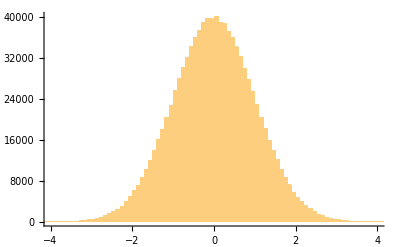

```mathematica
rns=Table[Table[RandomVariate[NormalDistribution[]],{j,1,4},{k,1,4}],{i,1,1000000}];
Histogram[rns[[All,1,1]],100,PlotRange->{{-4,4},All}]
```

```mathematica
NoisyInvEff=Inverse[Eff+EffErr*#]&/@rns;
```

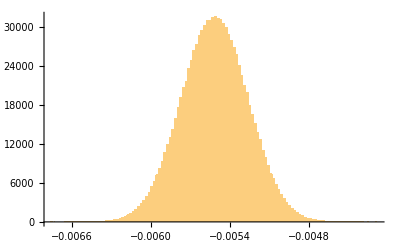

```mathematica
Histogram[NoisyInvEff[[All,3,4]],100,PlotRange->{All,All}]
```

```mathematica
NoisyInvEffSort=Table[NoisyInvEff[[All,i,j]],{i,1,4},{j,1,4}];
Inverse[Eff]
A=Mean[#]&/@#&/@NoisyInvEffSort;
A//MatrixForm
EffErr//MatrixForm
sA=StandardDeviation[#]&/@#&/@NoisyInvEffSort;
sA//MatrixForm
```

{{2.55485,0.00040029,-0.0124034,0.000035662},{-0.000315962,1.12279,-0.00443317,0.0000221928},{-0.0355172,-0.0383692,1.10206,-0.00551583},{0.0000686127,0.0000741222,-0.00212898,1.03417}}

(2.55489 | 0.000400241 | -0.0124032 | 0.0000356116
-0.000315861 | 1.12279 | -0.00443343 | 0.0000221933
-0.0355179 | -0.0383696 | 1.10206 | -0.0055156
0.0000686078 | 0.0000741164 | -0.00212878 | 1.03418)

(0.001594 | 0.000011 | 0.000235 | 0.00001
0.000041 | 0.001015 | 0.000212 | 0.
0.000365 | 0.000564 | 0.001029 | 0.000221
0. | 0. | 0.000153 | 0.000569)

(0.0103971 | 0.0000398779 | 0.000662995 | 0.0000267937
0.000117988 | 0.00127931 | 0.000262416 | 1.65981×10^-6
0.00103749 | 0.000701046 | 0.00125047 | 0.0002517
5.96119×10^-6 | 6.2146×10^-6 | 0.000174165 | 0.000608897)

```mathematica
Round[Eff.A,10^-4]//MatrixForm
AccountingForm[MatrixForm[sA],2]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(0.01 | 0.00004 | 0.00066 | 0.000027
0.00012 | 0.0013 | 0.00026 | 0.0000017
0.001 | 0.0007 | 0.0013 | 0.00025
0.000006 | 0.0000062 | 0.00017 | 0.00061)

```mathematica
Export[NotebookDirectory[]<>"../calc/invEfficencies_Math.txt",A,"Table"];
sAexp=SetPrecision[sA,2];
Export[NotebookDirectory[]<>"../calc/invEfficencies_error_Math.txt",ToString[AccountingForm[#,2]]&/@#&/@sA,"Table"];
```

```mathematica
Quiet[100EffErr/Eff]//MatrixForm
Abs[100sA/Inverse[Eff]]//MatrixForm
```

(0.407179 | 100. | 5.33364 | 100.
25.625 | 0.113947 | 5.91353 | Indeterminate
2.89178 | 1.81859 | 0.113367 | 4.56612
Indeterminate | Indeterminate | 8.19058 | 0.0588439)

(0.406956 | 9.96226 | 5.34527 | 75.1322
37.3425 | 0.113941 | 5.91939 | 7.47903
2.92108 | 1.82711 | 0.113466 | 4.56323
8.68816 | 8.38426 | 8.18071 | 0.0588776)